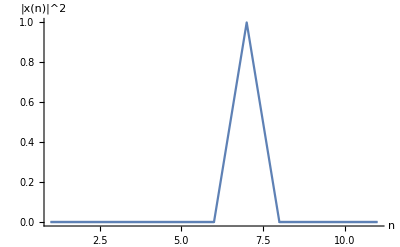

```mathematica
(*Poincare recurrence of a harmonic chain*)
num = 11;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
alpha =Take[nulist,{1,num-1}]/nulist[[num]];
x1 = 6;x2  =7;x3 = 8;
x0 = Table[0,{i,1, num}];
For[i = x1, i≤ x2, i++, x0[[i]]= (i - x1)/(x2 - x1);];
For[i = x2, i≤x3, i++, x0[[i]]=(x3-i)/(x3 - x2);];
basis = Sqrt[2/(num+1)]*Table[Sin[i*j*Pi/(num+1)],{i,1,num},{j,1,num}];
proj = basis.x0;
Q = 10^30;
A = Table[0,{i, 1,  num-1},{j,1,num-1}];
A[[1, 1]] = 1; 
For[i=1, i ≤num-2, i++, A[[1, i+1]]=Round[Q*alpha[[i]]];];
For[i=2, i≤num-1, i++, A[[i,i]] = Q; ];
bb = LatticeReduce[A];
q = Abs[bb[[1,1]]];
error = Abs[N[q*alpha - Round[q* alpha],200]];
time = N[q*2*Pi/(nulist[[num]]), 200] ;
x1 = N[basis.(Cos[time*nulist]*proj),200];
proj;
h1 = ListPlot[x0, Joined->True];
h2 = ListPlot[x1, Joined->True];
Show[h1, h2, AxesLabel -> {"n","|x(n)|^2"}, PlotRange -> All]
```

```mathematica
Cos[time*nulist]
```

```mathematica
A
```

84350294911456044599486768675168

0.002721799176662840767971275107961158196589829049142715205338737954425747185714900371862252507645305382666669706086166531875010074739055376662342618656731265705116159068739943951160240904751505289034954

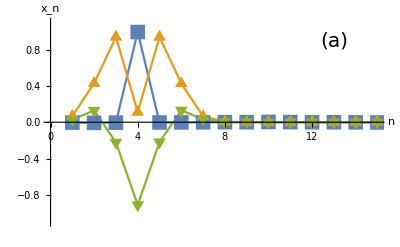

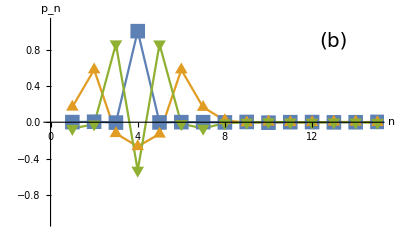

```mathematica
(*Poincare recurrence of a harmonic chain*)
num = 15;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
alpha =Take[nulist,{1,num-1}]/nulist[[num]];
ind1 =4;
ind2 = ind1 ;
x0p0 = Table[0,{i,1, num},{j,1,2}];
x1p1 =x0p0;
x0p0[[ind1, 1]]=1;
x0p0[[ind2,2]]= 1;
basis = Sqrt[2/(num+1)]*Table[Sin[i*j*Pi/(num+1)],{i,1,num},{j,1,num}];
proj0 = basis.x0p0;
projtr = Table[0,{i,1,num},{j, 1,2}];
projp1 = Table[0,{i,1,num},{j, 1,2}];
projm1 = Table[0,{i,1,num},{j, 1,2}];
proj13 = Table[0,{i,1,num},{j, 1,2}];
Q = 10^35;
A = Table[0,{i, 1,  num},{j,1,num}];
A[[1, 1]] = 1; 
For[i=1, i ≤num-1, i++, A[[1, i+1]]=Round[Q*alpha[[i]]];];
For[i=2, i≤num, i++, A[[i,i]] = Q; ];
bb = LatticeReduce[A];
q = Abs[bb[[1,1]]]
error = Abs[N[q*alpha - Round[q* alpha],200]];
Max[error]
rectime= N[q*2*Pi/(nulist[[num]]), 200] ;
time = rectime;
For[i=1, i≤num, i++, projtr[[i]]= {Cos[time*nulist[[i]]]*proj0[[i,1]]+Sin[time*nulist[[i]]]*proj0[[i,2]]/nulist[[i]],-Sin[time*nulist[[i]]]*nulist[[i]]*proj0[[i,1]]+Cos[time*nulist[[i]]]*proj0[[i,2]]};];
time = rectime +2;
For[i=1, i≤num, i++, projp1[[i]]= {Cos[time*nulist[[i]]]*proj0[[i,1]]+Sin[time*nulist[[i]]]*proj0[[i,2]]/nulist[[i]],-Sin[time*nulist[[i]]]*nulist[[i]]*proj0[[i,1]]+Cos[time*nulist[[i]]]*proj0[[i,2]]};];
time = rectime -2;
For[i=1, i≤num, i++, projm1[[i]]= {Cos[time*nulist[[i]]]*proj0[[i,1]]+Sin[time*nulist[[i]]]*proj0[[i,2]]/nulist[[i]],-Sin[time*nulist[[i]]]*nulist[[i]]*proj0[[i,1]]+Cos[time*nulist[[i]]]*proj0[[i,2]]};];
time = 2* rectime /3;
For[i=1, i≤num, i++, proj13[[i]]= {Cos[time*nulist[[i]]]*proj0[[i,1]]+Sin[time*nulist[[i]]]*proj0[[i,2]]/nulist[[i]],-Sin[time*nulist[[i]]]*nulist[[i]]*proj0[[i,1]]+Cos[time*nulist[[i]]]*proj0[[i,2]]};];
xptr= basis.projtr;
xpp1 = basis.projp1;
xpm1 = basis.projm1;
xp13 = basis.proj13;
h1 = ListLinePlot[{xptr[[All, 1]],xpp1[[All,1]],xpm1[[All,1]]} ,AxesLabel -> {"n","x_n"},   TicksStyle->Medium,AxesStyle->20, PlotRange->{{0, 15}, {-1.1, 1.1}}, PlotMarkers->{{ "■",15}, { "▲",15}, {"▼",15}}];
h11 = Graphics[Text[Style["(a)",20],{13,0.9}]];
Show[h1,h11]
h21 = ListLinePlot[{xptr[[All, 2]],xpp1[[All,2]],xpm1[[All,2]]} ,AxesLabel -> {"n","p_n"},  TicksStyle->Medium, AxesStyle->20,PlotRange->{{0, 15}, {-1.1, 1.1}}, PlotMarkers->{{ "■",15}, { "▲",15}, {"▼",15}}];
h22 = Graphics[Text[Style["(b)",20],{13,0.9}]];
Show[h21,h22]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.txt"]]]
```

```mathematica
SystemOpen["test.txt"]
```

```mathematica
A
```

```mathematica
bb
```

```mathematica
num = 10;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
alpha =Take[nulist,{2,num}]/nulist[[1]];
ind  =5;
x0p0 = Table[0,{i,1, num},{j,1,2}];
x1p1 =x0p0;
x0p0[[ind, 1]]=1;
x0p0[[ind,2]]=1;
basis = Sqrt[2/(num+1)]*Table[Sin[i*j*Pi/(num+1)],{i,1,num},{j,1,num}];
proj0 = basis.x0p0;
proj1 = Table[0,{i,1,num},{j, 1,2}];
Q = 10^45;
A = Table[0,{i, 1,  num-1},{j,1,num-1}];
A[[1, 1]] = 1; 
For[i=1, i ≤num-2, i++, A[[1, i+1]]=Round[Q*alpha[[i]]];];
For[i=2, i≤num-1, i++, A[[i,i]] = Q; ];
bb = LatticeReduce[A];
q = Abs[bb[[9,1]]]
N[Norm[bb[[1]]]]
error = Abs[N[q*alpha - Round[q* alpha],200]]
```

7862671717318363692808167502321010180469

8.93631×10^39

{3.1181427646881530872250950524998827225763114110699925694991819353964729796421939186192067616360806508336123932921422657170949846524872826736526095894607945492360880248054031828760530883948945012793524×10^-6,5.3256660899256734924922156620538033018550581212992995312080369913458909181242983598820802175894275913910751643468940412088443488855617571746020259774519150061316185647584175245061396171436890671706645×10^-6,5.8173230179680130530799490496527790683049540623216585524157509010264702721052627908270884111573332126371769163044569320077903164264965552900017169813213820190428306533169586509068730272372220561841283×10^-6,1.9634649983691917617221502613293996673536774524107931693148852867978765761525564357267098651706442469313409506891071613250301302672841680302537427317056974432082679753628475593252286103153622018612512×10^-7,4.2184781888766951936888762797762784787471498331453735246725321668748370431357681425416256395226374134511155853887777032948263247656475540616094580614544911206022555429006681823765337955121300997941881×10^-6,3.0127137099332780236265823075808627165329483783918538730558463493128177211721265932094132852746466967088714877382012891224109204320451763347332132845552495588314112663749413464067603573379159932468407×10^-6,4.3285817611371366668011089296776278029669426377068621856374115676313512808894642175213988444448644932337430981656316431494714002466040824227554113296711561590436518903565821107202450489960188293300149×10^-6,7.6086165547453831702926601218661919834209428155178504633178625237261476838307749070763408053586543034280116391844253283672029755038525029032166384835801810561723939337840677218356652824513801077523383×10^-7,0.48048679251526090194440612253335010855593382882655553356027630878107488872853100881178621015842707157702494235318712295439654623673669281876637240480969739802757207103445219167332188124972982311381683}

```mathematica
num = 5;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
alpha =Take[nulist,{2,num}]/nulist[[1]]
Q = 10^15;
A = Table[0,{i, 1,  num-1},{j,1,num-1}];
A[[1, 1]] = 1; 
For[i=1, i ≤num-2, i++, A[[1, i+1]]=Round[Q*alpha[[i]]];];
For[i=2, i≤num-1, i++, A[[i,i]] = Q; ];
bb = LatticeReduce[A];
q = Abs[bb[[1,1]]]
N[Norm[bb[[1]]]]
error = Abs[N[q*alpha - Round[q* alpha],200]]
```

{(√2)/(-1+√3),2/(-1+√3),(√6)/(-1+√3),(1+√3)/(-1+√3)}

132936965836

1.64649×10^11

{0.00011700815667355173249235380252052292928833259355682034025654491725926217609044142607435286081354090890022482053844640964859071037476574572273419729773389491135697335973484450674000491411985634608759626,0.000050986534278229089343637652157791791878374011035528811973472965560857211863788670029529950372979248425564740512275200671520131572562689890834522197801655619622453002462889486139496817247262150993741432,0.00012542002582688236143278311120668021389270675925449915282177098453001794699807515210936773296878352315482810582107518511814995768931905951539149892589675584570473648302773388450153751157665175521847388,0.000050986534278229089343637652157791791878374011035528811973472965560857211863788670029529950372979248425564740512275200671520131572562689890834522197801655619622453002462889486139496817247262150993741432}

```mathematica
num =10;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
alpha =Take[nulist,{2,num}]/nulist[[1]]
Q = 10^20;
A = Table[0,{i, 1,  num-1},{j,1,num-1}];
A[[1, 1]] = 1; 
For[i=1, i ≤num-2, i++, A[[1, i+1]]=Round[Q*alpha[[i]]];];
For[i=2, i≤num-1, i++, A[[i,i]] = Q; ];
bb = LatticeReduce[A];
q = Abs[bb[[1,1]]]
error = Abs[N[q*alpha - Round[q* alpha],200]]
```

{Csc[π/22] Sin[π/11],Csc[π/22] Sin[(3 π)/22],Csc[π/22] Sin[(2 π)/11],Csc[π/22] Sin[(5 π)/22],Cos[(5 π)/22] Csc[π/22],Cos[(2 π)/11] Csc[π/22],Cos[(3 π)/22] Csc[π/22],Cos[π/11] Csc[π/22],Cot[π/22]}

48076903213428513

{0.00026746508663985034560692626346614769281381868715142654898098745912540281020641979295145979064587605321622326784319880354089662825681021183191224055098801145337639945437973726169932377642995270791847134,5.6377611175775928085917421664315826939438912209423913828219996445298325414664523526038208058519023880727944062222953034395035760378522874416009431798149631053347670909766024766345897744933255125845753×10^-6,0.00009898015839531445771709595605369251721328282409445433521295361001021344847757797922426171180802293873356577249202754341168871536177137246984834446814366997027442190690305642592718380675668083933397065,0.0020911303325927038248780612453177095516725086324493413237717995158976425530300920780107962811068894249804697650359078908921978958660750995769373306668835156699641038078165323926601884546274616541840373,0.0014271716676167566608609058471720419280623670509240356333944699340300189439808919431978354581355962962675803364294231924235408432180168539325874133534508027070337055349880626783340400761685378742314878,0.0020023547925742408351965685647614221337972761152571383721704018327319881673705541086670420645770835336709796128558323582439962945512437374672383467652617396307275336690213625850924753823778826982720707,0.0012208587109426045316329435615872645296241202605117448733538229515099151647605988183783968425277864250947779929586447469053977772285395933371798418388112660690361499575247561405436698476258060313661071,0.0018905089355375625916137323040575239016193462812895850216442762702033189933914075934870088296174665460514266740326020252405257010007256234987006321581009091806275417048054767159465544739108253292005853,0.25587009785939527712255148027913025900290559067561800128060682786208136937958150926092843161349161363667508160030987888480126065441050864345312195403885481109844995210528242666358763125166444112761323}

```mathematica
Block[{$MaxExtraPrecision=1000},
num =10;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
alpha =Delete[nulist,1]/nulist[[1]];
Q = 10^40;
A = Table[0,{i, 1,  num},{j,1,num}];
A[[1, 1]] = 1; 
For[i=1, i ≤num-1, i++, A[[1, i+1]]=Round[Q*alpha[[i]]];];
For[i=2, i≤num, i++, A[[i,i]] = Q; ];
bb = LatticeReduce[A];
q = Abs[bb[[1,1]]];
error = Abs[N[q*alpha - Round[q* alpha],200]];];
q
error 
N[ Norm[bb[[1]]]/(4*Det[A]^{1/9})]
```

34109437675034567588946795420853397

{0.000023084673651620859731613624803406051043336081412737282024157354128281555803669670550059026600218962801535628048463988063564553065250074779877103610694075701738920914127905965917869450840963104601471112,0.000031669793832904700605838430025687036553816995082117560350946548623500730887826375884934296247496339619839909396982918478591818171310905565068083999395122957556549081854038045432365268223972722422223406,0.00004226043784812050143955071179119603811519910372758591898753046822158260812853813979221429018906641486658562317823283015903995117255423517386479125355816566539569845722812695007186697910770302109691985,0.00003584379524201119274193383125436775324942813666810291006116234466124565841779190892427124379835884827468732734144167051381264073699905296459749498314033456584389636286451976263931519809342794700323811,0.000012802815863107909756016938246884703102028152384833514319405489002656416571531756993768507286479555377257711607281939099819417005879162521497734888535439845080570074824478138277316031208365825466124487,0.000041989063028423680111769408277949694040150411654074058726538748611794219848975406180685451186135576881949841915885124491184890134375049848115018617343525290535050939327593996345842982585588119636161264,7.8463869799712434975709868666240841659281882592077397802598704571540198397531250260163027624479746863354879662322735392378123797964134978721198466940005565848974166261047274937082564423260704216753079×10^-6,0.000022881532009293520682803090043864435096460625886559130326759753141935943815216841539271484626876546662288195573447878218481348488532881008682927607996816240738734015520611648341826004159416762532020332,0.000016383841069538217983217199802285487557470285269228354167241178353860672867015594723830350333187930926916337797038855622872069583670943743315206694651669102190692465339494191746999362456797662808329464}

{0.0000214867}

```mathematica
FindIntegerNullVector[alpha]
```

FindIntegerNullVector::rnfu: FindIntegerNullVector has not found an integer null vector for {Csc[π/22] Sin[π/11],Csc[π/22] Sin[(3 π)/22],Csc[π/22] Sin[(2 π)/11],Csc[π/22] Sin[(5 π)/22],Cos[(5 π)/22] Csc[π/22],Cos[(2 π)/11] Csc[π/22],Cos[(3 π)/22] Csc[π/22],Cos[π/11] Csc[π/22],Cot[π/22]}.

FindIntegerNullVector[{Csc[π/22] Sin[π/11],Csc[π/22] Sin[(3 π)/22],Csc[π/22] Sin[(2 π)/11],Csc[π/22] Sin[(5 π)/22],Cos[(5 π)/22] Csc[π/22],Cos[(2 π)/11] Csc[π/22],Cos[(3 π)/22] Csc[π/22],Cos[π/11] Csc[π/22],Cot[π/22]}]

```mathematica
A
```

{{1,1000000000000000000000000000000000000000000000000000000000000,1474501270492847362742756403700029053779762075961121256283006,1918985947228994779780736114132655398124909696844323910088990,2324405603978054844832858438011465441093758770325600460906434,2682507065662362337723623297838735435026584996841075797285300,2986000419201363930290828091644717894139196966299568395443005,3228707415119564907894586259065242504492492095518180765301581,3405687238889250009048130346648848831957299986121828140977934},{0,1000000000000000000000000000000000000000000000000000000000000,0,0,0,0,0,0,0},{0,0,1000000000000000000000000000000000000000000000000000000000000,0,0,0,0,0,0},{0,0,0,1000000000000000000000000000000000000000000000000000000000000,0,0,0,0,0},{0,0,0,0,1000000000000000000000000000000000000000000000000000000000000,0,0,0,0},{0,0,0,0,0,1000000000000000000000000000000000000000000000000000000000000,0,0,0},{0,0,0,0,0,0,1000000000000000000000000000000000000000000000000000000000000,0,0},{0,0,0,0,0,0,0,1000000000000000000000000000000000000000000000000000000000000,0},{0,0,0,0,0,0,0,0,1000000000000000000000000000000000000000000000000000000000000}}

```mathematica
a = {1,4}
```

{1,4}

```mathematica
b ={a,1}
```

{{1,4},1}

```mathematica
FindIntegerNullVector[Union[alpha,{ 1}]]
```

FindIntegerNullVector::rnfu: FindIntegerNullVector has not found an integer null vector for {1,Cot[π/11],Cos[π/22] Csc[π/11],Cos[(3 π)/22] Csc[π/11],Cos[(2 π)/11] Csc[π/11],Cos[(5 π)/22] Csc[π/11],Csc[π/11] Sin[π/22],Csc[π/11] Sin[(3 π)/22],Csc[π/11] Sin[(2 π)/11],Csc[π/11] Sin[(5 π)/22]}.

FindIntegerNullVector[{1,Cot[π/11],Cos[π/22] Csc[π/11],Cos[(3 π)/22] Csc[π/11],Cos[(2 π)/11] Csc[π/11],Cos[(5 π)/22] Csc[π/11],Csc[π/11] Sin[π/22],Csc[π/11] Sin[(3 π)/22],Csc[π/11] Sin[(2 π)/11],Csc[π/11] Sin[(5 π)/22]}]

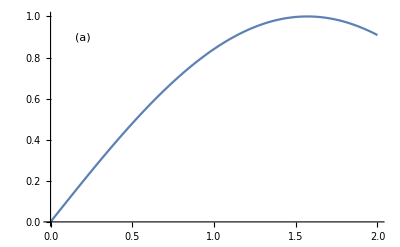

```mathematica
t1 = Plot[Sin[x],{x, 0, 2}];
t2 = Graphics[Text["(a)", {0.2, 0.9}]];
Show[t1, t2]
```